## RIng of mass with global sound speed

```mathematica
ρ[r_]:=ρ0 Exp[-(r/rc-1)^2/2]+ρ1
```

(cs^2 r (-r+rc) ρ0)/(rc^2 (ρ0+ⅇ^(1/2 (-1+r/rc)^2) ρ1))

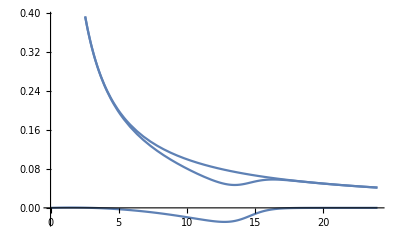

```mathematica
cs^2 r/ρ[r] ρ'[r]//FullSimplify
Plot[{%,1/r,%+1/r}/.{rc->3,ρ0->1,ρ1->0.001,cs->0.05},{r,0,24}]
```

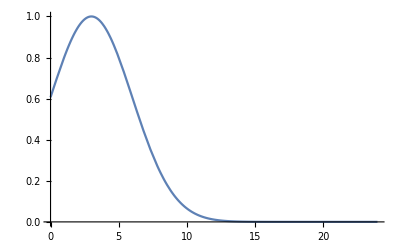

```mathematica
Plot[ρ[r]/.{rc->3,ρ0->1,ρ1->0.0001,cs->0.05},{r,0,24}]
```

```mathematica
(cs^2 r (-r+rc) (ρ[r]-ρ1))/(rc^2 ρ[r])==(cs^2 r (-r+rc) ρ0)/(rc^2 (ρ0+ⅇ^(1/2 (-1+r/rc)^2) ρ1))//FullSimplify
```

True

## Ring of mass with (roughly) uniform Mach number

```mathematica
ρ[r_]:=ρ0 Exp[-(r/rc-1)^2/2]+ρ1
cs2[r_]:=GM/r 1/Ma^2
```

```mathematica
dpdr=r/ρ[r] D[ρ[r] cs2[r],r]//FullSimplify
```

(GM (-1/r+((-r+rc) ρ0)/(rc^2 (ρ0+ⅇ^(1/2 (-1+r/rc)^2) ρ1))))/Ma^2

```mathematica
GM/(Ma^2 r) (x(1-x) (1-ρ1/ρ[r])-1)
```

(GM (-1+(1-x) x (1-ρ1/(ⅇ^(-1/2 (-1+r/rc)^2) ρ0+ρ1))))/(Ma^2 r)

```mathematica
(1/Ma^2 GM/r (x(1-x) (1-ρ1/ρ[r])-1)/.x->r/rc)==dpdr//Simplify
```

True

## Total disk mass

```mathematica
Integrate[2π r ρ[r]/.ρ1->0,{r,0,∞}]
```

ConditionalExpression[(π rc^2 ρ0 (2+√(2 ⅇ π) (√(1/rc^2) rc+Erf[1/(√2)])))/(√ⅇ),(Re[rc]<0&&Re[rc^2]≥0)||Re[rc^2]>0]

```mathematica
FullSimplify[(π rc^2 ρ0 (2+√(2 ⅇ π) (√(1/rc^2) rc+Erf[1/(√2)])))/(√ⅇ),Assumptions->rc>0]//N
```

17.0618 rc^2 ρ0